# Etude de cas: dimensionnement d'une colonne à garnissage

### Paramètres généraux

#### Constantes

```mathematica
R=8.314 (*J/mol K*);
MMk2hpo4= 174(*g/mol*);
MMna2hpo4h20=138 (*g/mol*);
MMna2hpo4= 142 (*g/mol*);
MMnacl=58 (*g/mol*);
MMnh4cl=53 (*g/mol*);
MMkh2po4=136 (*g/mol*);
MMmgcl26h2o=203 (*g/mol*);
MMcacl22h2o=147 (*g/mol*);
MMh2o = 18 (*g/mol*);
MMh2=2(*g/mol*);
MMco2=44(*g/mol*);
MMch4=16(*g/mol*);
MMair=29 (*g/mol*);
gz=9.81 (*m/s^2*);
```

#### Paramètres opératoires

```mathematica
T=273.15 (*K*);
p0=151988 (*Pa*);
QgNin=50 (*cm^3 STP/min*);
QlinMax=5 (*L/min*);
QLin = 4.5 (*L/min*);
QlinMin =2.5 (*L/min*);

(*Temps de résidence gaz*)
Tgazmin=0.5 (*h*);
Tgazmax = 12(*h*);

(*proportion de phase in*)
(*mélange H2/CO2*)
yh2=0.08;
yco2=0.02;
yair=0.9;

(*concentration initiale de liquide*)
Cik2=4000 (*mg/L*);
Cina2=2700(*mg/L*);
Cina=1100(*mg/L*);
Cinh4=1000(*mg/L*);
Cikh2=500(*mg/L*);
Cinacl=400(*mg/L*);
Cimg=330(*mg/L*);
Cica=50(*mg/L*);

(*proportion de phase out*)
(*mélange H2/CO2*)
ych4=1;
```

### Question 1 : détermination du débit de liquide minimum

#### Conversion du débit de gaz à l'entrée en débit massique et masse volumique

```mathematica
MMgazin= yh2 MMh2+yco2 MMco2 + yair MMair(*g/mol*);
QGin= (QgNin 10^-6)/60 101325/(R 273.15) MMgazin(*g/s*);
ρGin= pin/(R T) MMgazin(*kg/m^3*);
```

#### Composition massique gaz entrée et sortie

```mathematica
xCO2in=(yco2 MMco2)/(yco2 MMco2+yh2 MMh2+yair MMair) (*g/g gaz*);
xCO2out=0 (*g/g gaz*); (*pas forcément 0*)

xH2in =(yh2 MMh2)/(yco2 MMco2+yh2 MMh2+yair MMair) (*g/g gaz*);
xH2out=0(*g/g gaz*); (*pas forcément 0*)
```

#### Bilan gaz

```mathematica
QGout=0 (*g/s*); (*pas obligé d'être à 0*)
Tco2=QGin-QGout (*g/s*);
```

#### Paramètres du fluide (considère de l’eau au début)

```mathematica
ρw=997.13 (*kg/m^3*);
ρg=3.50149 (*kg/m^3*);
μw=0.891 10^-3 (*Pa.s*); (*visco à 25°C,https://www.thermexcel.com/french/tables/eau_atm.htm*)
μg=9.06 10^-4 (*Pa.s*); (*visco à 25°C*)
σ=69.6 10^-3 (*N/m*); (*tension de surface du fluide*)
ϵl=0.016; (*proportion de liquide dans reac*)
```

#### Bilan liquide

```mathematica
QmLin= (QLin 10^-3)/60 ρw 10^3(*g/s*);
QLout=QmLin+Tco2(*g/s*);
```

#### Résultats

```mathematica
Print["Débit massique de gaz à l'entrée: ",QGin," kg/s - Masse volumique: ",ρGin," kg/m^3"];
Print["Fraction massique dioxyde de carbone gaz entrée: ",xCO2in];
Print["Fraction massique dioxyde de carbone gaz sortie: ",xCO2out];
Print["Débit massique de transfert gaz-liquide de CO_2: ",Tco2," kg/s"];
Print["Débit de liquide nécessaire à l'entrée: ",QLin," kg/s"];

Print["Débit de liquide à la sortie: ",QLout," kg/s"];
```

Débit massique de gaz à l'entrée: 0.0010091 kg/s - Masse volumique: 0.0119508 pin kg/m^3

Fraction massique dioxyde de carbone gaz entrée: 0.0324245

Fraction massique dioxyde de carbone gaz sortie: 0

Débit massique de transfert gaz-liquide de CO_2: 0.0010091 kg/s

Débit de liquide nécessaire à l'entrée: 4.5 kg/s

Débit de liquide à la sortie: 0.0010091+0.075 ρl kg/s

#### Paramètres du garnissage n°1 : Hillflow rings 25-7, blanc

```mathematica
ρs= 90 (*kg/m.b3*); (*weight or density*)
dp=25 10^-3 (*m*);
ϵ=0.90 (*m^3 vide/m^3 appareil, void fraction*);
Fp=320 (*m^2/m^3*); 
Fp2=312/ϵ^3; (*a_{RFK}/ϵ^3, difficulty of the fluid to flow through the bed*)
Ap=312 (*m^2/m^3*);
σc=0.033 (*N/m*); (*Tension de surface critique pour les élément de garnissage*)
```

#### Paramètre du garnissage n°2 : RFK25L

```mathematica
aRFK= 312 (*m.b2/m.b3*); (*specific surface area*)
ρRFK = 71 (*kg/m.b3*);
ϵRFK = 1-0.945; (*Void fraction*)
```

#### Paramètres physico-chimiques du transfert

```mathematica
Dco2g=6.55 10^-8 √T (*m^2/s*);
Dco2l=3 10^-5 Exp[-3096/T] (*m^2/s*);
Dh2l= 5.13 10^-9(*m.b2/s*);

Dh2g=0.756 10^-4(*m.b2/s*); (*https://www.engineeringtoolbox.com/air-diffusion-coefficient-gas-mixture-temperature-d_2010.html*)
hco2=1.5 10^-5 T Exp[1375/T] (*-*);
hH2=hco2 (*-*);
kin=10^(7.9-2152/T) (*m^3/(mol*s)*);

(*Henry law : C(M)=k(M/atm)*P(atm) *)
kh2 = 7.7 10^-6 (*mol/L/atm*); (*Constante Henry H2 à T=25°C*)
kco2=  3.4 10^-4 (*Constante Henry CO2 à T*); (*Constante Henry CO2 à T*)
pin=1.5 (*atm*);
Ch2sat= kh2 pin yh2(*mol/m.b3*);
Cco2sat= kco2 pin yco2(*mol/m.b3*);
```

#### Paramètres de la colonne

```mathematica
Ω=Pi ((20. 10^-2)/2)^2(*m*);
hreac = 99 10^-2 (*m*);

Vsg= (QgNin 10^-6)/(60. Ω) (*m/s*); (*--> huge problem for master thesis*)
Vsl=(QLin 10^-3)/(3600. Ω)(*m/s*);
ΔpOverL=205 (*Pa/m*);
```

### Equations pour le transfer de matière au sein de la colonne

#### Coefficients pour le transfert gaz-liquide sans réaction

```mathematica
kG=(Ap Dco2g) 5.23 (Ap dp)^-2 ((Vsg ρGin)/(μg Ap))^0.7 (μg/(ρGin Dco2g))^0.5 (*m/s*);  
kGH2=(Ap Dh2g) 5.23 (Ap dp)^-2 ((Vsg ρGin)/(μg Ap))^0.7 (μg/(ρGin Dh2g))^0.5 (*m/s*);
kL=(Ap Dco2l) 0.0051 (Ap dp)^0.4 ((Vsl ρw)/(μw Ap))^1.33 (μw/(ρw Dco2l))^0.5 ((Vsl^2 Ap)/gz)^-0.33 (*m/s*); 
kLH2=(Ap Dh2l) 0.0051 (Ap dp)^0.4 ((Vsl ρw)/(μw Ap))^1.33 (μw/(ρw Dh2l))^0.5 ((Vsl^2 Ap)/gz)^-0.33(*m/s*);
Areacor=Ap (1-Exp[-1.45 (σc/σ)^0.75 ((Vsl ρw)/(μw Ap))^0.1 ((Vsl^2 ρw)/(σ Ap))^0.2 ((Vsl^2 Ap)/gz)^-0.05]) (*m^2/m^3*);
Print["Coefficient transfert CO2 gaz: ",kG," m/s"];
Print["Coefficient transfert CO2 liquide: ",kL," m/s"];
Print["Coefficient transfert H2 gaz: ",kGH2," m/s"];
Print["Coefficient transfert H2 liquide: ",kLH2," m/s"];
Print["Densité d'aire interfaciale: ",Areacor," m^2 interface/m^3 lit"];
```

Coefficient transfert CO2 gaz: 5.69666×10^-7 m/s

Coefficient transfert CO2 liquide: 1.24521×10^-6 m/s

Coefficient transfert H2 gaz: 4.76058×10^-6 m/s

Coefficient transfert H2 liquide: 4.70956×10^-6 m/s

Densité d'aire interfaciale: 17.8792 m^2 interface/m^3 lit

#### Pressure Drop

```mathematica
Vsge=0.03 (*m/s*);(*depuis les valeurs théoriques du livre pour dp = 25 x10^-2*)
π1= Fp/gz ρg/ρw Vsg^2;
π1e=Fp/gz ρg/ρw Vsge^2;
π2=Vsl/Vsg √(ρw/ρg);
A1=21.79-36.19 π2^0.25+16.60 π2^0.5; (*corrélation du livre*) 
A2=7.06+10.30 π2^0.25-10.36 π2^0.5;

ΔP=((98π1)/π1e (A1+A2 π1/π1e) ) hreac(*Pa/m*);
(*Pression du au gaz*)
Pgaz=ρg gz hreac (*Pa*);
Print["La perte de charge est estimée à, ΔP=",ΔP , "[Pa]"]
Print["La pression en bas de la colonne du à la présence du gaz est de Pgaz=", Pgaz, "[Pa]"]
```

La perte de charge est estimée à, ΔP=0.00183045[Pa]

La pression en bas de la colonne du à la présence du gaz est de Pgaz=34.0061[Pa]

#### Résolution du système d'équations

```mathematica
p[z]=p0-ΔpOverL z (*Pa*); (*considère la même perte de charge que dans le problème*)
yCO2[z]=(xCO2[z]/MMco2)/(xCO2[z]/MMco2+xH2[z]/MMh2);
yH2[z]=(xH2[z]/MMh2)/(xCO2[z]/MMco2+xH2[z]/MMh2);
Eacc=1; (*considère être égale à 1 pour le moment*)
Kgl[z]=(hco2 Eacc kG kL)/(hco2 Eacc kL+kG) (*unité ?*);
KglH2[z]=(hH2 Eacc kG kL)/(hH2 Eacc kL+kG); (*-*)
Fco2[z]=Areacor Ω Kgl[z]  p[z]/(R T) yCO2[z] (*mol/(s.m)*);  
Fh2[z]=Areacor  Ω KglH2[z]  p[z]/(R T) yH2[z] (*mol/(s.m)*);
EqQgaz=Qgaz'[z]== 0(*kg/(s.m)*); (*-MMco2 Fco2[z] -MMh2 Fh2[z]*)
EqxCO2=xCO2'[z]==-(MMco2 Fco2[z])/Qgaz[z] (1-xCO2[z]) (*kg CO2/(kg gaz.m)*); (*changer en volume de liquide*)
EqxH2=xH2'[z]==-(MMh2 Fh2[z])/Qgaz[z] (1-xH2[z]) (*kg CO2/(kg gaz.m)*);
EqQliq=Qliq'[z]==0 (*kg/(s.m)*);


EqxCO2o=xCO2[0]==xCO2in (*kg CO2/kg gaz*);
EqxH2o=xH2[0]==xH2in (*kg H2/ kg gaz*);
EqQgazo=Qgaz[0]==QGin  (*kg gaz/s*);
EqQliqo=Qliq[0]==QLout (*kg/s*);


Soluce=NDSolve[{EqQgaz,EqxCO2,EqxH2,EqxCO2o,EqxH2o,EqQgazo},{xCO2[z],xH2[z], Qgaz[z]},{z,0,hreac}];
```

#### Résultats

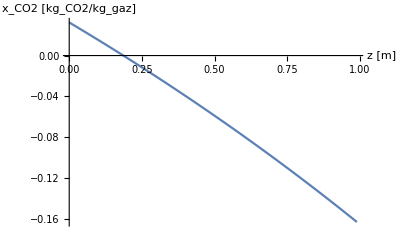

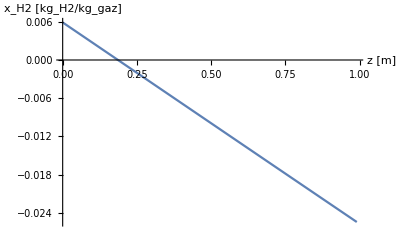

```mathematica
Plot[(xCO2[z]/.(Soluce[[1]])),{z,0,hreac},PlotRange->Full,AxesLabel->{"z [m]","x_CO2 [kg_CO2/kg_gaz]"}]
Plot[(xH2[z]/.(Soluce[[1]])),{z,0,hreac}, PlotRange -> Full, AxesLabel ->{"z [m]","x_H2 [kg_H2/kg_gaz]"}]
```

#### Autre Resol

Declaration des paramètres

```mathematica
m=0.14 (*gH2/gX/h*); (*maintenance rate*)
Yxh2=0.22 (*gx/gh2*);
Yco2h2=5.70 (*gco2/gh2*); 
Ych4h2=1.92 (*gch4/gh2*);
Ymco2h2=5.5 (*gco2/gh2*);
```

Equations

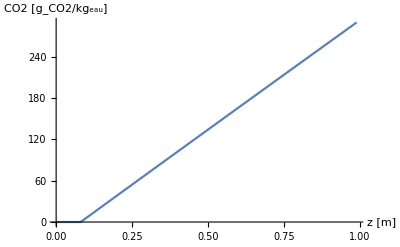

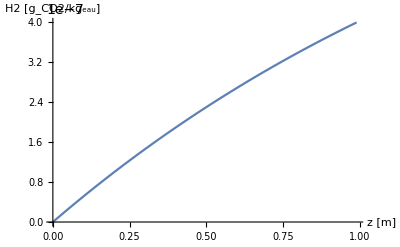

```mathematica
φH2[z]=(kL Areacor (Ch2sat-H2[z]))/(ϵl Xbio[z]);
r1[z]= φH2[z]-m;
r2[z]=m;
r3[z]=0;
EqCO2= CO2'[z]==(Kgl[z] (Cco2sat-CO2[z])+ϵl (Yco2h2 r1[z]+Yco2h2 r2[z]))/Vsl;
EqH2=H2'[z]==(KglH2[z] (Ch2sat-H2[z])+ϵl φH2[z] Xbio[z])/Vsl;
EqCH4=CH4'[z]==(ϵl (Ych4h2 r1[z]+Ych4h2 r2[z]))/Vsl;
EqXbio=Xbio'[z]==(ϵl Yxh2 (r1[z]-r3[z]))/Vsl; (*variation selon z ?? no sens*)
Sol= NDSolve[{EqH2,EqCO2,EqCH4, EqXbio, H2[0]==0,CO2[0]==0, CH4[0]==0, Xbio[0]==1},{H2[z],CO2[z],CH4[z],Xbio[z]},{z,0,hreac}];


Plot[(CO2[z]/.(Sol[[1]])),{z,0,hreac},PlotRange->Full,AxesLabel->{"z [m]","CO2 [g_CO2/kg_eau]"}]
Plot[(H2[z]/.(Sol[[1]])),{z,0,hreac},PlotRange->Full,AxesLabel->{"z [m]","H2 [g_CO2/kg_eau]"}]
```